```mathematica
Needs["PlotLegends`"]
Λ = 1.
1.
Λ^2
1.
NN = 50
cc[k_]  :=  Exp[ (ⅈ 2 π k)/NN]
circ= Array[cc, NN, 0];
```

1.

1.

1.

«1 more identical outputs»

50

```mathematica
sys[u_, m_] :={(σ - m) ∑_(k=1)^(NN-1) (Log [  - (σ - m)^2 + (σ - m circ[[k+1]])(σ - Conjugate[m circ[[k+1]]])] - Log [Λ^2]) - ∑_(k=1)^(NN-1) (σ - m circ[[k+1]]) Log [ 1 + (- (σ - m)^2)/((σ - m circ[[k+1]])(σ - Conjugate[m circ[[k+1]]]))] + NN u σ== 0 };
```

```mathematica
sol[u_, m_]:=FindRoot[sys[u,m],{σ,0.9m}]
```

```mathematica
sig[u_,m_]:= σ /. sol[u, m]
(* nn[u_, m_] := n /. sol[u,m] *)
```

```mathematica
sol[4.0, 5.0]
```

{σ→2.01084+1.4153×10^-18 ⅈ}

```mathematica
m = 10.
```

10.

```mathematica
slin[u_] :=  m - (m u / 2)/(Log [ m / Λ ]);
```

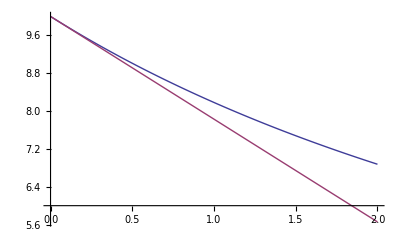

```mathematica
Plot[{sig[u,m], slin[u]},{u,0.0,2.0}]
```

```mathematica
Seqn[u_,μ_] := { ( 1. + u + Log[μ^2]) S == μ ( 1. + Log[ μ S ] ) }
Ssol[u_, μ_]:=FindRoot[Seqn[u,μ],{S,0.9  μ}]
SS[u_, μ_] := S /. Ssol[u, μ]
```

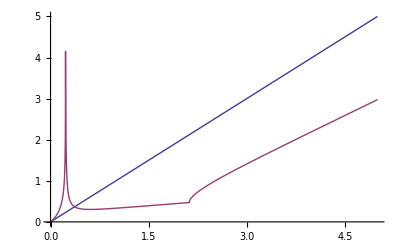

```mathematica
Plot[{μ, SS[2., μ]}, {μ, 0.0 / Λ, 5.0 / Λ }]
```

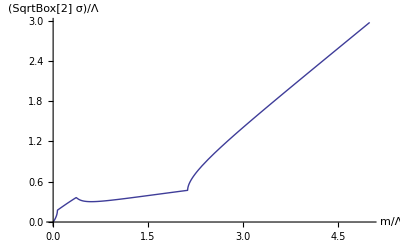

```mathematica
Plot[sig[2.0,m],{m,0.0, 5.0},PlotStyle->Thick, AxesLabel->{Style["m/Λ",FontSize->15], Style["(SqrtBox[2] σ)/Λ",FontSize->15]}]
```

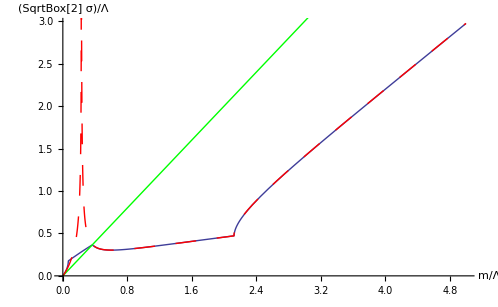

```mathematica
Show[%,Plot[{μ, SS[2., μ]}, {μ, 0.0 / Λ, 5.0 / Λ },PlotStyle->{Green,{Thick,Red,Dashing[{0.03}]}}]]
```

```mathematica
DD[u_, μ_] := - ( SS[u, μ] - μ )^2
```

```mathematica
Nsq[u_, μ_] :=  Log [ SS[u,μ] μ ]
```

```mathematica
NNNsq[u_,μ_] :=1/NN∑_(k=1)^(NN-1) Log[  DD[u,μ] + ( SS[u,μ] - μ circ[[ k+1 ]] )  (SS[u, μ] - μ Conjugate[ circ[[k+1]] ] ) ]
```

```mathematica
DD[2.,3.0]
```

-2.52963

```mathematica
Nsq[2., 3.0]
```

1.44186

```mathematica
NNNsq[2., 3.0]
```

1.5695+0. ⅈ

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

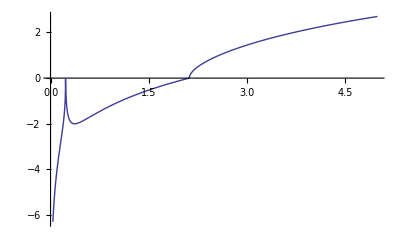

```mathematica
Plot[ Nsq[2., μ], {μ, 0./Λ, 5./Λ }]
```

```mathematica
rsolve[u_] := NSolve[ x - Log[x] == 1. + u, x ]
r1[u_] :=  x /. rsolve[u][[1]]
r2[u_] :=  x /. rsolve[u][[2]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Part::partw: Part 2 of {{x → 0.9995483140731668`}} does not exist.

ReplaceAll::reps: {{{x → 0.9995483140731668`}} ⟦ 2 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{x → 0.6198246622568275`}} does not exist.

ReplaceAll::reps: {{{x → 0.6198246622568275`}} ⟦ 2 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{x → 0.48885745944031767`}} does not exist.

General::stop: Further output of Part will be suppressed during this calculation.

ReplaceAll::reps: {{{x → 0.48885745944031767`}} ⟦ 2 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll will be suppressed during this calculation.

Plot::exclul: {Im[x/. {{Rule[« 2 »]}} ⟦ 2 ⟧] - 0} must be a list of equalities or real-valued functions.

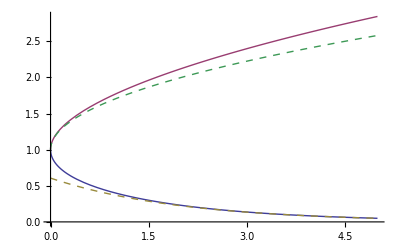

```mathematica
Plot[{Sqrt[r1[u]],Sqrt[r2[u]], ⅇ^(-(u+1)/2), 1 + √(u/2)}, {u, 0.0, 5.0}, PlotStyle->{Thick,Thick,Dashed,Dashed}]
```

```mathematica
NSolve[ x  - Log[x] == 1. + 2., x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.0524691},{x→4.50524}}

```mathematica
√0.05246909745771487
```

0.229061

```mathematica
√4.505241495792883
```

2.12256

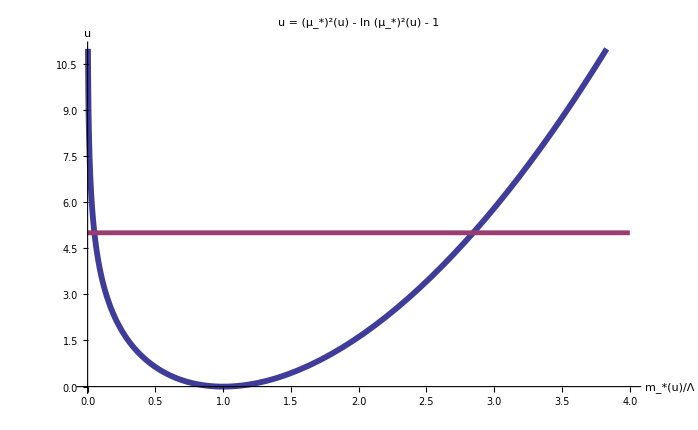

```mathematica
Plot[ {μ^2 - Log [ μ^2]  - 1 , 5.0}, {μ, 0., 4.0},PlotStyle->{Thickness[0.006], {Thickness[0.005]}}, LabelStyle->{Directive[FontSize->15]}, 
PlotLabel->Style["u     =     (μ_*)^2(u)   -   ln (μ_*)^2(u)   -   1",FontSize->21],
AxesLabel->{Style["m_*(u)/Λ",FontSize->20], Style["u", FontSize->20]}]
```

```mathematica
Plot[ {μ^2 - Log [ μ^2]  - 1 , 5.0}, {μ, 0., 2.0},PlotRange->{0.,2.5},Filling->Axis, PlotStyle->{Thickness[0.006], {Thickness[0.005]}}, LabelStyle->{Directive[FontSize->15]}, 
AxesLabel->{Style["m/Λ",FontSize->20], Style["u", FontSize->20]}]
```

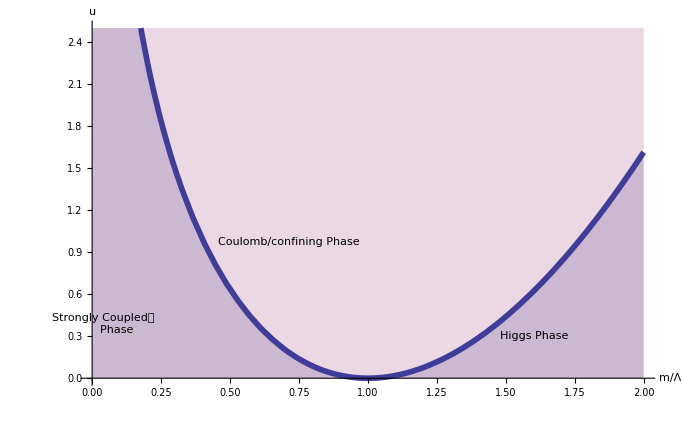

```mathematica
Plot[{SS[2., μ], Nsq[2., μ]}, {μ, Sqrt[r2[2.]], 5.0}, PlotStyle->{Thick,{Thick,Dashed}}, 
      AxesLabel->{Style["m/Λ",FontSize->15],Style["√2σ/Λ and (4  π)/N|n|^2", FontSize->15]} , 
         PlotLegend->{Style["√2σ/Λ", FontSize->15],Style["(4  π)/N|n|^2", FontSize->15]}]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

General::stop: Further output of InverseFunction will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve will be suppressed during this calculation.

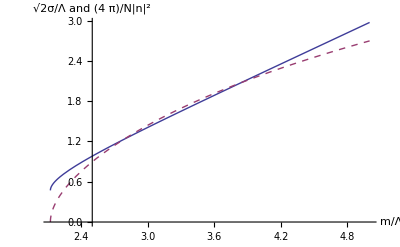

```mathematica
confE[μ_] := 1. - μ^2 + μ^2 Log[ μ^2]
Efunc[u_,μ_] :=- 1/NN∑_(k=1)^(NN-1) ((DD[u,μ] + ( SS[u,μ] - μ circ[[k+1]]) ( SS[u,μ] - μ Conjugate[circ[[k+1]]])) Log[ DD[u,μ] + ( SS[u,μ] - μ circ[[k+1]]) ( SS[u,μ] - μ Conjugate[circ[[k+1]]])] ) + 1/NN ∑_(k=1)^(NN-1) (( SS[u,μ] - μ circ[[k+1]]) ( SS[u,μ] - μ Conjugate[circ[[k+1]]]) Log[ ( SS[u,μ] - μ circ[[k+1]]) ( SS[u,μ] - μ Conjugate[circ[[k+1]]])] ) + DD[u,μ]  + u ( SS[u,μ])^2
Eanalyt[u_, μ_] := (μ^2 - (SS[u,μ])^2) Log [ μ^2 ] - (μ - SS[u,μ])^2 - u (SS[u,μ])^2
```

```mathematica
Plot[{Efunc[2.,μ],1. - μ^2 + μ^2 Log[ μ^2], Eanalyt[2., μ]}, {μ, 2.0, 2.3}, AxesLabel->{Style["m/Λ",FontSize->15],Style["(4  π)/NE/Λ^2", FontSize->15]} ,
             PlotStyle->{Thick,Thick,{Thick,Dashed}},PlotLegend->{Style["Higgs/num",FontSize->15],Style["Coulomb",FontSize->15],
                                                                                                                                            Style["Higgs/s-analyt",FontSize->15]}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

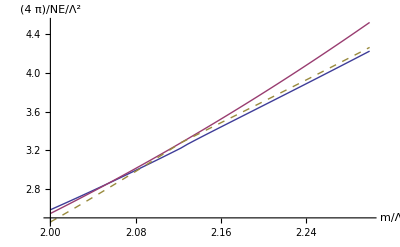

```mathematica
Plot[{1. - μ^2 + μ^2 Log[ μ^2], Eanalyt[2., μ]}, {μ, 1.5, 3.0}, AxesLabel->{Style["m/Λ",FontSize->15],Style["(4π)/NE/Λ^2", FontSize->15]} ,LabelStyle->{Directive[FontSize->15]},
             PlotStyle->{Thickness[0.006],{Thickness[0.006],Dashing[{0.03,0.005}]}},PlotLegend->{Style["Coulomb",FontSize->15],Style["Higgs",FontSize->15]},
LegendSize->0.5]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

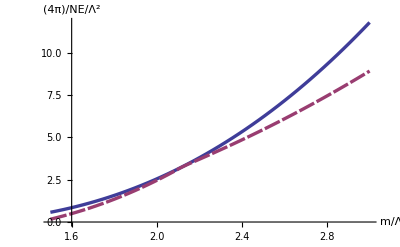

```mathematica
Efunc[2., Sqrt[r2[2.0]]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

3.22147+0. ⅈ

```mathematica
Eanalyt[2.0,Sqrt[r2[2.0]]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

3.27623

```mathematica
confE[Sqrt[r2[2.0]]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

3.27623

```mathematica
DDi[s_,u_, μ_] := - ( s - μ )^2
Eimplicit[s_,u_, μ_] := - 1/NN∑_(k=1)^(NN-1) ((DDi[s,u,μ] + ( s - μ circ[[k+1]]) ( s - μ Conjugate[circ[[k+1]]])) Log[ DDi[s,u,μ] + ( s - μ circ[[k+1]]) ( s - μ Conjugate[circ[[k+1]]])] ) + 1/NN ∑_(k=1)^(NN-1) (( s - μ circ[[k+1]]) ( s - μ Conjugate[circ[[k+1]]]) Log[ ( s - μ circ[[k+1]]) ( s - μ Conjugate[circ[[k+1]]])] ) + DDi[s,u,μ]  + u s^2
```

```mathematica
Eimplicit[1./Sqrt[r2[2.0]], 2.0, Sqrt[r2[2.0]] ]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

3.22147+0. ⅈ

```mathematica
u=2.0
```

2.

```mathematica
Subscript[m, min] = 1.0;
Subscript[m, max]= 3.0;
MM = 75;
dm = (Subscript[m, max] - Subscript[m, min])/MM;
mpos =Table[Null,{MM}];
ssig = Table[Null,{MM}];
ddd = Table[Null, {MM}];
EEE = Table[Null,{MM}];
sigcorr = Table[Null, {MM}];
assig = Table[Null, {MM}];
```

```mathematica
abssq[k_,l_] := ( ssig[[l+1]] - mpos[[l+1]] circ[[k+1]])Conjugate[ ssig[[l+1]] - mpos[[l+1]] circ[[k+1]]]
```

```mathematica
For [ l = 0, l < MM, l++, 
mpos[[l+1]] = Subscript[m, min] + dm l;
ssig[[l+1]] = SS[u, mpos[[l+1]] ];
ddd[[l+1]] = DD[u,mpos[[l+1]] ];
EEE[[l+1]] = 1/NN∑_(k=0)^(NN-1) (abssq[k,l] Log[ abssq[k,l]] -( ddd[[l+1]] + abssq[k,l]) Log [ ddd[[l+1]] +abssq[k,l]] ) + ddd[[l+1]] + u (Abs[ssig[[l+1]]])^2;
EEE[[l+1]] = 1/Λ^2 EEE[[l+1]];
];
```

FindRoot::nlnum: The function value {-0.8946394843421737` + 0.9` (1.`  + u)} is not a list of numbers with dimensions {1} at {S} = {0.9`}.

ReplaceAll::reps: {FindRoot[Seqn[u, 1.`], {S, 0.9` 1.`}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.8946394843421737` + 0.9` (1.`  + u)} is not a list of numbers with dimensions {1} at {S} = {0.9`}.

ReplaceAll::reps: {FindRoot[Seqn[u, 1.`], {S, 0.9` 1.`}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.8946394843421737` + 0.9` (1.`  + u)} is not a list of numbers with dimensions {1} at {S} = {0.9`}.

General::stop: Further output of FindRoot will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Seqn[u, 1.`], {S, 0.9` 1.`}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll will be suppressed during this calculation.

$Aborted

```mathematica
Evsm = Partition[Riffle[mpos,EEE ],2];
mvsm = Partition[Riffle[mpos,mpos],2];
sigvsm = Partition[Riffle[mpos,ssig],2];
sigcorrvsm = Partition[Riffle[mpos,sigcorr],2];
dvsm = Partition[Riffle[mpos,ddd],2];
```

∞::indet: Indeterminate expression 0.` (-∞) encountered.

∞::indet: Indeterminate expression 0.` ∞ encountered.

Power::infy: Infinite expression 1/(0.`  + 0.` ⅈ)^2 encountered.

∞::indet: Indeterminate expression 0.` ComplexInfinity encountered.

General::stop: Further output of indet will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {σ} = {0.`}.

ReplaceAll::reps: {FindRoot[sys[2.`, 0.`], {σ, 0.9` 0.`}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Power::infy: Infinite expression 1/(0.`  + 0.` ⅈ)^2 encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {σ} = {0.`}.

ReplaceAll::reps: {FindRoot[sys[2.`, 0.`], {σ, 0.9` 0.`}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Power::infy: Infinite expression 1/(0.`  + 0.` ⅈ)^2 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {σ} = {0.`}.

General::stop: Further output of FindRoot will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[sys[2.`, 0.`], {σ, 0.9` 0.`}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll will be suppressed during this calculation.